```mathematica
Ori=Import["G:\\毕个业\\basic\\pack\\pack12\\Ori.csv"];
Rc=Import["G:\\毕个业\\basic\\pack\\pack12\\Rc.csv"];
CyList=Range[Dimensions[Rc][[2]]];
CyFigList=Range[Dimensions[Rc][[2]]];
d=30.4*2;
h=4.7*2;

For[i=1,i<=Dimensions[Rc][[2]],i++,
startP=Rc[[All,i]]-    Ori [[All,i]]*h/2;
endP=Rc[[All,i]]+    Ori [[All,i]]*h/2;
CyList[[i]]=Cylinder[{startP,endP},d/2]];
For[i=1,i<=Dimensions[Rc][[2]],i++,CyFigList[[i]]=Graphics3D[CyList[[i]]]];
Show[CyFigList]
cav=RegionUnion[CyList];
```

-Graphics3D-

```mathematica
line1=Region[InfiniteLine[{{0,0,0},{3,2,3}}]];
sol=Solve[p∈line1∧p∈cav,p]
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

```mathematica
{{p->ConditionalExpression[{p3,0.6666666666666666 p3,p3}, 81.42720151717695≤p3≤90.94867648850806||93.78430038627276≤p3≤103.2660776966077||215.6661612274345≤p3≤222.46339878695574||241.27147537518644≤p3≤255.68931870085507||298.23878643264527≤p3≤302.3417816379729||306.7476984369753≤p3≤328.4335682754209]}}
```

```mathematica
MinDis=Range[Dimensions[Rc][[2]]];
For[i=1,i<=Dimensions[Rc][[2]],i++,MinDis[[i]]=RegionDistance[CyList[[i]],{100,100,100}]];
Min[MinDis]
```

5.39399

```mathematica
minX=Min[Rc[[1]]]+d;maxX= Max[Rc[[1]]]-d;
minY= Min[Rc[[2]]]+d;maxY= Max[Rc[[2]]]-d;
minZ=Min[Rc[[3]]]+d;maxZ= Max[Rc[[3]]]-d;
testnum=100;
MinDisList=Range[testnum];
Parallelize[
For[i=1,i<=testnum,i++,
x=RandomReal[{minX,maxX}];y=RandomReal[{minY,maxY}];z=RandomReal[{minZ,maxZ}];

For[j=1,j<=Dimensions[Rc][[2]],j++,
MinDis[[j]]=RegionDistance[CyList[[j]],{x,y,z}]
];
MinDisList[[i]]=Min[MinDis];
];
];
MinDisList
```

{1.02922,4.10937,3.60741,0.139707,1.32251,3.65192,2.70828,9.67008,0.331162,10.9026,1.72935,6.54775,0.,5.86746,0.,3.32271,1.12346,0.,1.68263,0.,0.,2.86765,5.25411,0.,6.72445,8.30514,7.78507,2.87169,0.,0.,0.,4.47863,0.824115,0.612496,10.3991,14.0196,0.669157,11.6168,0.,10.1727,4.34687,8.14122,0.,12.1884,1.42223,0.,10.5143,6.10863,1.94978,2.20537,1.3419,8.9189,5.14579,14.1618,0.,1.90829,8.79559,0.,0.,0.,5.28407,1.4983,0.,7.008,0.86507,3.25707,3.64228,0.,2.14761,14.7482,0.,0.,0.877983,7.67632,0.910619,0.958598,9.20275,5.81291,6.99329,5.02964,0.,0.508451,5.98216,0.,2.01112,0.,1.70923,1.92835,3.412,6.91271,6.80224,7.67573,4.59512,2.25847,0.,1.26126,4.09949,0.,0.,19.3592}

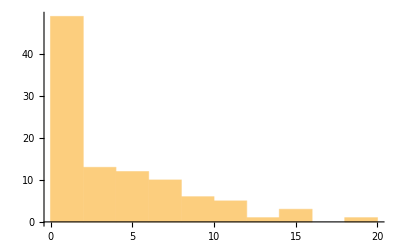

```mathematica
Histogram[%150]
```

```mathematica
sol[[1]][[1]][[2]][[2]]
```

68.4436≤p3≤80.4503||82.5946≤p3≤92.2526||95.1191≤p3≤95.6869||112.451≤p3≤115.772||117.472≤p3≤123.901||125.47≤p3≤131.927||134.468≤p3≤140.915||196.621≤p3≤216.756||224.72≤p3≤230.337||239.132≤p3≤243.196||244.623≤p3≤250.421||251.523≤p3≤257.292||270.832≤p3≤279.495||282.014≤p3≤290.962||314.602≤p3≤336.501||345.168≤p3≤346.691